# Cryptic transmission of SARS-CoV-2 in Washington State

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/ncov-cryptic-transmission/beast-wa-clade

## Options

```mathematica
colors=Table[ColorData["Rainbow"][i],{i,{0.3,0.7,0.95}}];
```

### Functions

```mathematica
numericToCalendar[numDate_]:=DatePlus["2019-01-01",Quantity[numDate-2019,"Years"]]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

```mathematica
numberToString[num_]:=If[Negative[num],"-"<>StringDrop[ToString[num],1],ToString[num]]
```

```mathematica
Clear[frameTicks]
```

```mathematica
frameTicks[xMin_,xMax_,yMin_,yMax_,xTicksStep_,yTicksStep_]:={{Table[{i, numberToString[i], {0, 0.01}}, {i, Floor[yMin,yTicksStep], Ceiling[yMax,yTicksStep], yTicksStep}], None}, {Table[{i, numberToString[i], {0, 0.01}}, {i,Floor[xMin,xTicksStep], Ceiling[xMax,xTicksStep], xTicksStep}], None}}
```

```mathematica
frameTicks[]:={{None, None}, {Table[{i, If[EvenQ[i],numberToString[i],""], If[EvenQ[i],{0, 0.01},{0, 0.005}]}, {i,1994, 2014}], None}}
```

```mathematica
frameTicks[yMin_,yMax_,yTicksStep_]:={{Table[{i, numberToString[i], {0, 0.01}}, {i, Floor[yMin,yTicksStep], Ceiling[yMax,yTicksStep], yTicksStep}], None}, {Table[{i, If[EvenQ[i],numberToString[i],""], If[EvenQ[i],{0, 0.01},{0, 0.005}]}, {i,1994, 2014}], None}}
```

### Options

```mathematica
fontSize=11;
```

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[RegionPlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[DateHistogram,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListContourPlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400];
```

```mathematica
SetOptions[ContourPlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameStyle->Black,ImageSize->400];
```

```mathematica
SetOptions[DiscretePlot,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->400,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->400,FrameStyle->Black,PlotRange->{0,All}];
```

```mathematica
SetOptions[Histogram,LabelStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->400,PlotRange->{0,All},ChartBaseStyle->EdgeForm[Thin]];
```

```mathematica
SetOptions[SmoothDensityHistogram,FrameStyle->Directive[Black,FontSize->fontSize,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},FrameTicksStyle->Black,FrameStyle->Black,ImageSize->400,PlotRange->{0,All}];
```

```mathematica
SetOptions[ArrayPlot,ImageSize->400,Frame->False,Mesh->True,MeshStyle->Thin];
```

## Exponential growth

With growth parameter

```mathematica
x0*ⅇ^(k t)
```

ⅇ^(k t) x0

```mathematica
x==ⅇ^(k t)/popSize
```

x==ⅇ^(k t)/popSize

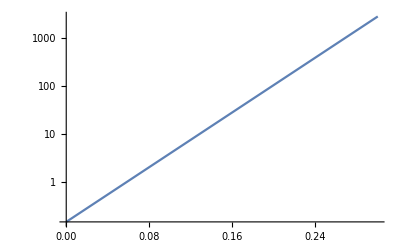

```mathematica
LogPlot[ⅇ^(33. t)/7,{t,0,0.3}]
```

With doubling time parameter

```mathematica
x0*2^(t/T)
```

2^(t/T) x0

```mathematica
1*2^(26/3.4)
```

200.444

```mathematica
growthRateInYearsToDoublingTimeInDays[growthRate_]:=365*Log[2]/growthRate
```

```mathematica
growthRateInYearsToDoublingTimeInDays[82.1]
```

3.08159

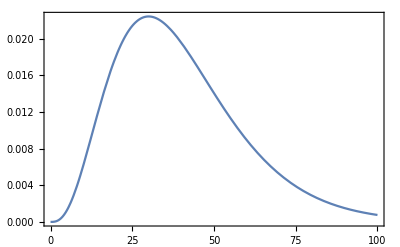

```mathematica
Plot[PDF[GammaDistribution[4,10],x],{x,0,100}]
```

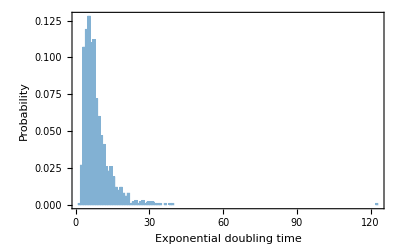

```mathematica
Histogram[Map[growthRateInYearsToDoublingTimeInDays,RandomVariate[GammaDistribution[4,10],1000]],{1},"Probability",PlotRange->{0,All},PlotTheme->"FullAxes",FrameLabel->{"Exponential doubling time","Probability"},ChartStyle->Lighter[colors[[1]],0.3]]
```

## Data

```mathematica
log=Import["ncov-wa-clade.log","Table"][[4;;-1]];
```

```mathematica
header=log[[1]]
```

{state,joint,prior,likelihood,treeModel.rootHeight,age(root),treeLength,exponential.popSize,exponential.growthRate,kappa,frequencies1,frequencies2,frequencies3,frequencies4,alpha,clock.rate,treeLikelihood,coalescent}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{state→1,joint→2,prior→3,likelihood→4,treeModel.rootHeight→5,age(root)→6,treeLength→7,exponential.popSize→8,exponential.growthRate→9,kappa→10,frequencies1→11,frequencies2→12,frequencies3→13,frequencies4→14,alpha→15,clock.rate→16,treeLikelihood→17,coalescent→18}

```mathematica
burnin=1000;
```

```mathematica
skip=1;
```

```mathematica
data=log[[burnin;;-1;;skip]];
```

```mathematica
length=Length[data]
```

9003

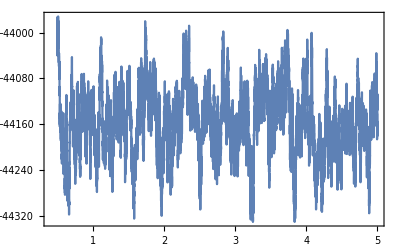

```mathematica
ListLinePlot[data[[All,{"state"/.headerRules,"joint"/.headerRules}]],PlotRange->All]
```

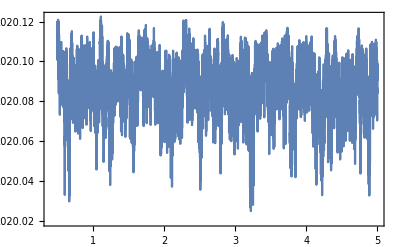

```mathematica
ListLinePlot[data[[All,{"state"/.headerRules,"age(root)"/.headerRules}]],PlotRange->All]
```

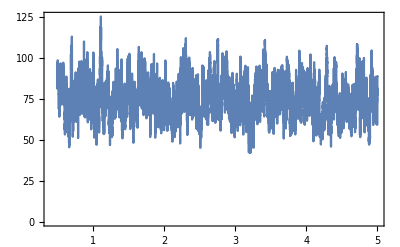

```mathematica
ListLinePlot[data[[All,{"state"/.headerRules,"exponential.growthRate"/.headerRules}]],PlotRange->All]
```

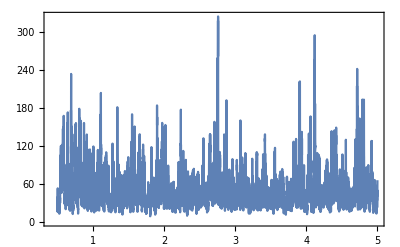

```mathematica
ListLinePlot[data[[All,{"state"/.headerRules,"exponential.popSize"/.headerRules}]],PlotRange->All]
```

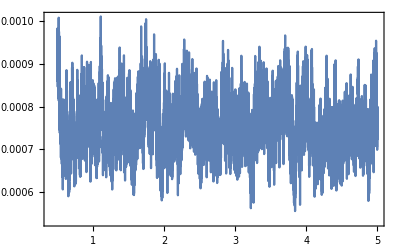

```mathematica
ListLinePlot[data[[All,{"state"/.headerRules,"clock.rate"/.headerRules}]],PlotRange->All]
```

## Growth rate

```mathematica
Median[data[[All,"exponential.growthRate"/.headerRules]]]
```

74.5906

```mathematica
Quantile[data[[All,"exponential.growthRate"/.headerRules]],0.025]
```

54.7345

```mathematica
Quantile[data[[All,"exponential.growthRate"/.headerRules]],0.975]
```

97.5744

```mathematica
median=growthRateInYearsToDoublingTimeInDays@Median[data[[All,"exponential.growthRate"/.headerRules]]]
```

3.39183

```mathematica
upper=growthRateInYearsToDoublingTimeInDays@Quantile[data[[All,"exponential.growthRate"/.headerRules]],0.025]
```

4.62229

```mathematica
lower=growthRateInYearsToDoublingTimeInDays@Quantile[data[[All,"exponential.growthRate"/.headerRules]],0.975]
```

2.59288

```mathematica
growthRateInYearsToDoublingTimeInDays@Quantile[data[[All,"exponential.growthRate"/.headerRules]],0.25]
```

3.77083

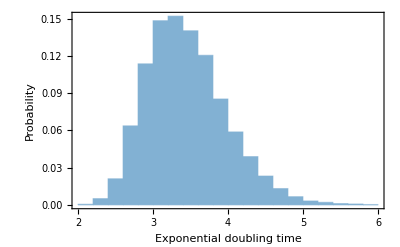

```mathematica
figGrowthRate=Histogram[Map[growthRateInYearsToDoublingTimeInDays,data[[All,"exponential.growthRate"/.headerRules]]],20,"Probability",PlotTheme->"FullAxes",FrameLabel->{"Exponential doubling time","Probability"},ChartStyle->Lighter[colors[[1]],0.3]]
```

```mathematica
smoothedHistogramHPD[data_,lower_,upper_,xMin_,xMax_,xLabel_,bandwidth_,ticks_]:=Module[{dist},
dist=SmoothKernelDistribution[data,{"Standardized",bandwidth}];
Plot[{PDF[dist,x],If[x<lower,PDF[dist,x],0],If[x≥lower&&x≤upper,PDF[dist,x],0],If[x>upper,PDF[dist,x],0]},{x,xMin,xMax},PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{xLabel,"Probability"},PlotStyle->{Darker[colors[[1]],0.3],None,None,None},AspectRatio->0.5,Filling->{2->{Bottom,GrayLevel[0.85]},3->{Bottom,Lighter[colors[[1]],0.78]},4->{Bottom,GrayLevel[0.85]}},FrameTicks->ticks]
]
```

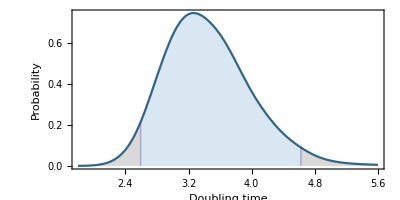

```mathematica
figGrowthRate=smoothedHistogramHPD[Map[growthRateInYearsToDoublingTimeInDays,data[[All,"exponential.growthRate"/.headerRules]]],lower,upper,1.8,5.6,"Doubling time",0.3,Automatic]
```

## TMRCA and clock rate

```mathematica
numericToCalendar@Median[data[[All,"age(root)"/.headerRules]]]
```

Sun 2 Feb 2020 19:07:15

```mathematica
numericToCalendar@Quantile[data[[All,"age(root)"/.headerRules]],0.025]
```

Wed 22 Jan 2020 11:21:52

```mathematica
numericToCalendar@Quantile[data[[All,"age(root)"/.headerRules]],0.975]
```

Mon 10 Feb 2020 08:00:09

```mathematica
tmrcaPosterior=Map[numericToCalendar,Cases[data[[All,"age(root)"/.headerRules]],x_/;x>2019.8]];
```

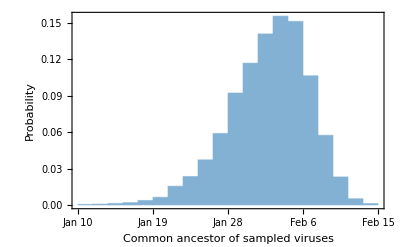

```mathematica
figTMRCA=DateHistogram[tmrcaPosterior,20,"Probability",PlotTheme->"FullAxes",FrameLabel->{"Common ancestor of sampled viruses","Probability"},ChartStyle->Lighter[colors[[1]],0.3]]
```

```mathematica
median=Median[data[[All,"age(root)"/.headerRules]]]
```

2020.09

```mathematica
lower=Quantile[data[[All,"age(root)"/.headerRules]],0.025]
```

2020.06

```mathematica
upper=Quantile[data[[All,"age(root)"/.headerRules]],0.975]
```

2020.11

```mathematica
ticks={{{2020.030,"Jan 12"},{2020.058,"Jan 22"},{2020.085,"Feb 1"},{2020.112,"Feb 11"}},Automatic}
```

{{{2020.03,Jan 12},{2020.06,Jan 22},{2020.09,Feb 1},{2020.11,Feb 11}},Automatic}

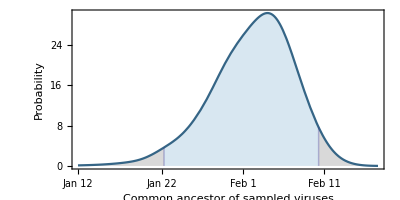

```mathematica
figTMRCA=smoothedHistogramHPD[data[[All,"age(root)"/.headerRules]],lower,upper,2020.03,2020.13,"Common ancestor of sampled viruses",0.3,ticks]
```

```mathematica
Export["figures/tmrca.png",figTMRCA,"png",ImageResolution->300]
```

figures/tmrca.png

```mathematica
Median[data[[All,"clock.rate"/.headerRules]]]
```

0.000754096

```mathematica
Quantile[data[[All,"clock.rate"/.headerRules]],0.025]
```

0.000638337

```mathematica
Quantile[data[[All,"clock.rate"/.headerRules]],0.975]
```

0.000886432

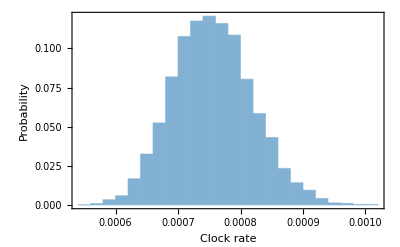

```mathematica
Histogram[data[[All,"clock.rate"/.headerRules]],20,"Probability",PlotTheme->"FullAxes",FrameLabel->{"Clock rate","Probability"},ChartStyle->Lighter[colors[[1]],0.3]]
```

```mathematica
InverseCDF[LogNormalDistribution[-7.131,0.05],0.5]
```

0.000799919

```mathematica
InverseCDF[LogNormalDistribution[-7.131,0.05],0.025]
```

0.000725247

```mathematica
InverseCDF[LogNormalDistribution[-7.131,0.05],0.975]
```

0.000882279

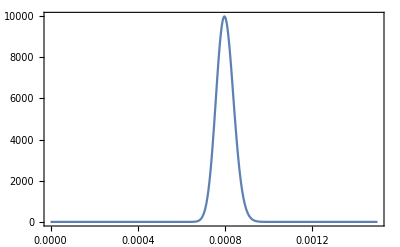

```mathematica
Plot[PDF[LogNormalDistribution[-7.131,0.05],x],{x,0,0.0015}]
```

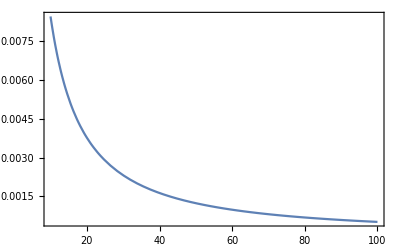

```mathematica
Plot[PDF[LogNormalDistribution[0,4],x],{x,10,100}]
```

## Composite

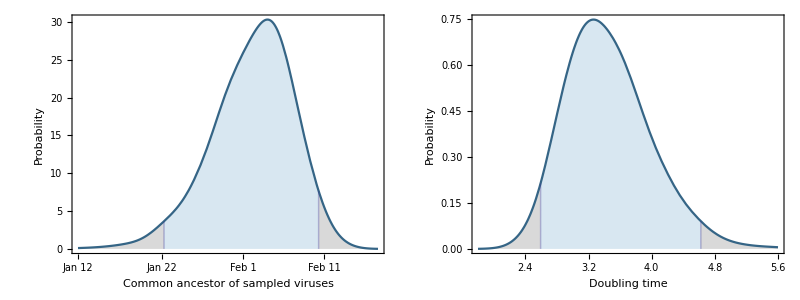

```mathematica
fig=Grid[{{figTMRCA,figGrowthRate}}]
```

```mathematica
Export["figures/ncov_wa_trmca_growth_rate.png",fig,"png",ImageResolution->300]
```

figures/ncov_wa_trmca_growth_rate.png

## Single parameters

```mathematica
startDate=2020.0;endDate=2020.2;
```

```mathematica
tau=0.020;
```

```mathematica
Table[numericToCalendar[t],{t,startDate,endDate,tau}]
```

{Wed 1 Jan 2020 00:00:00,Wed 8 Jan 2020 07:40:47,Wed 15 Jan 2020 15:21:35,Wed 22 Jan 2020 23:02:23,Thu 30 Jan 2020 06:43:11,Thu 6 Feb 2020 14:23:59,Thu 13 Feb 2020 22:04:47,Fri 21 Feb 2020 05:45:36,Fri 28 Feb 2020 13:26:24,Fri 6 Mar 2020 21:07:12,Sat 14 Mar 2020 04:48:00}

```mathematica
numericToCalendar[startDate]
```

Wed 1 Jan 2020 00:00:00

```mathematica
numericToCalendar[endDate]
```

Sat 14 Mar 2020 04:48:00

```mathematica
skylineNeTau[{tmrca_,popSize_,growthRate_}]:=Table[{t,ⅇ^(growthRate (t-tmrca))/popSize},{t,startDate,endDate,0.005}]
```

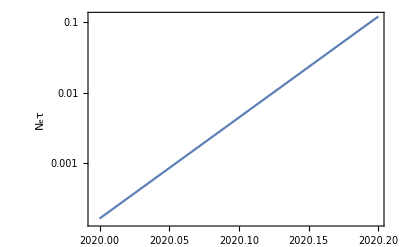

```mathematica
ListLogPlot[skylineNeTau[{Median[data[[All,"age(root)"/.headerRules]]],318.762,33.095}],Joined->True,FrameLabel->{"","N_eτ"}]
```

Assume a 7.5 day serial interval or a τ = 0.020 year serial interval.

If reported N_e τ is 2, it means that timescale of coalescence is 2 years. Divide by τ to get N_e.

Variance in offspring distribution required to get to population size N (prevalence). This is 2 for a standard epidemic compartmental model.

Variance σ^2 is R_0/ω+1. R0 is estimated to be 2.2. Omega is estimated to be 0.3.

```mathematica
meanR0=2.8;
```

```mathematica
varR0=meanR0^2/0.15+meanR0
```

55.0667

```mathematica
varR0/meanR0^2+1
```

8.02381

```mathematica
sigmaSquared[meanR0_,dispersion_]:=1/dispersion+1/meanR0+1
```

```mathematica
skylinePrev[{tmrca_,popSize_,growthRate_}]:=Module[{meanR0,k,σ2},
meanR0=RandomReal[{1.8,2.8}];
k=RandomReal[{0.3,0.5}];
σ2=sigmaSquared[meanR0,k];
Table[{t,σ2*ⅇ^(growthRate (t-tmrca))/(tau*popSize)},{t,startDate,endDate,0.005}]
]
```

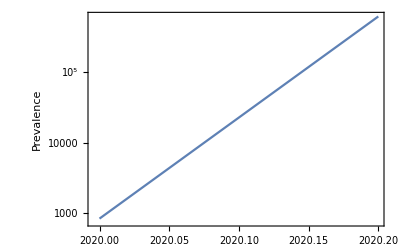

```mathematica
ListLogPlot[skylinePrev[{2019.784,318.762,33.095}],Joined->True,FrameLabel->{"","Prevalence"}]
```

## N_e τ and N_e Distributions

```mathematica
dateRangeToPlot={{2020,1,14},{2020,3,15}};
```

```mathematica
params[index_]:=data[[index,{"age(root)"/.headerRules,"exponential.popSize"/.headerRules,"exponential.growthRate"/.headerRules}]]
```

```mathematica
skylineNeTauList=Table[skylineNeTau[params[i]],{i,length}];
```

```mathematica
deltaT=0.004;
```

```mathematica
valuesAtTime[skylineList_,time_]:=Cases[Flatten[skylineList,1],{x_,y_}/;x≥time-deltaT&&x<time+deltaT][[All,2]]
```

```mathematica
quantileSkyline[skylineNeTau_,quantile_]:=Module[{skylineList},
skylineList=Table[skylineNeTau[params[i]],{i,length}];
Table[{numericToCalendar[t],Quantile[valuesAtTime[skylineList,t],quantile]},{t,startDate,endDate,0.005}]
]
```

```mathematica
medianNeTau=quantileSkyline[skylineNeTau,0.5];
```

```mathematica
lowerNeTau=quantileSkyline[skylineNeTau,0.025];
```

```mathematica
upperNeTau=quantileSkyline[skylineNeTau,0.975];
```

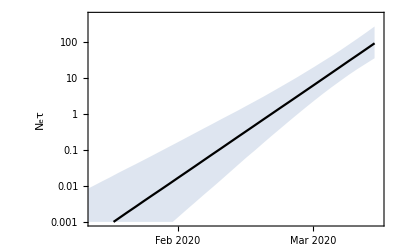

```mathematica
fig=DateListLogPlot[{lowerNeTau,medianNeTau,upperNeTau},Filling->1->{3},PlotStyle->{None,Black,None},PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","N_eτ"},PlotRange->{dateRangeToPlot,{0.001,500}}]
```

```mathematica
Export["figures/netau.png",fig,"png",ImageResolution->300]
```

figures/netau.png

```mathematica
medianPrev=quantileSkyline[skylinePrev,0.5];
```

```mathematica
lowerPrev=quantileSkyline[skylinePrev,0.025];s
```

s

```mathematica
upperPrev=quantileSkyline[skylinePrev,0.975];
```

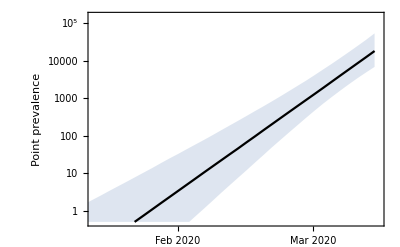

```mathematica
fig=DateListLogPlot[{lowerPrev,medianPrev,upperPrev},Filling->1->{3},PlotStyle->{None,Black,None},PlotTheme->"FullAxes",Frame->{True,True,False,False},FrameLabel->{"","Point prevalence"},PlotRange->{dateRangeToPlot,{0.5,150000}}]
```

```mathematica
Export["figures/prevalence.png",fig,"png",ImageResolution->300]
```

figures/prevalence.png

```mathematica
Last[medianPrev]
```

{Sat 14 Mar 2020 04:48:00,17975.9}

```mathematica
Last[lowerPrev]
```

{Sat 14 Mar 2020 04:48:00,6778.93}

```mathematica
Last[upperPrev]
```

{Sat 14 Mar 2020 04:48:00,53159.2}